```mathematica
SetOptions[SelectedNotebook[],PrintingStyleEnvironment->"Printout",ShowSyntaxStyles->True]
```

```mathematica
<<Notation`
```

```mathematica
Notation[Subscript[x_, n_] ⟺ x_[[n_]]]
```

```mathematica
χ[α_?NumericQ]:=Exp[-α r^2]; (* Basis function *)
α={13.00773,1.962079,0.444529,0.1219492}; (* Coefficients for the basis expansion *)
```

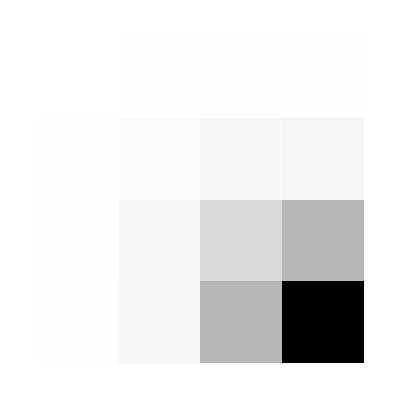
{True,-Graphics-,(0.0419641 | 0.0961392 | 0.112858 | 0.117043
0.0961392 | 0.716317 | 1.49148 | 1.85084
0.112858 | 1.49148 | 6.64247 | 13.0602
0.117043 | 1.85084 | 13.0602 | 46.2287)}

```mathematica
S=Array[(π/(Subscript[α, #1]+Subscript[α, #2]))^(3/2)&,{4,4}]; (* Overlap matrix *)
#[S]&/@{SymmetricMatrixQ,ArrayPlot,MatrixForm}
```

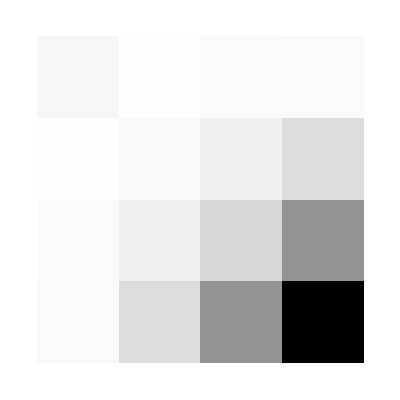
{True,-Graphics-,(0.577268 | 0.0720025 | -0.32154 | -0.436126
0.0720025 | 0.50705 | -0.989185 | -2.37742
-0.32154 | -0.989185 | -2.63808 | -7.34222
-0.436126 | -2.37742 | -7.34222 | -17.3052)}

```mathematica
H=Array[(3 π^(3/2) Subscript[α, #1] Subscript[α, #2])/(Subscript[α, #1]+Subscript[α, #2])^(5/2)-(2π)/(Subscript[α, #1]+Subscript[α, #2])&,{4,4}]; (* Hamiltonian matrix *)
#[H]&/@{SymmetricMatrixQ,ArrayPlot,MatrixForm}
```

```mathematica
{λ,ψ}=Eigensystem[{H,S}]; (* Eigenvalues and eigenvectors *)
λ
```

{21.1444,2.5923,-0.499278,0.113214}

```mathematica
ϵ=Min@λ Quantity[, "HartreeEnergy"] (* Ground-state eigenvalue *)
UnitConvert[ϵ, "Electronvolts"]
PercentForm@Abs[(ϵ-Quantity[-13.6058, "Electronvolts"])/Quantity[-13.6058, "Electronvolts"]](* Percent error on the reference value *)
```

-0.499278 E_h

-13.5861 eV

0.1451%

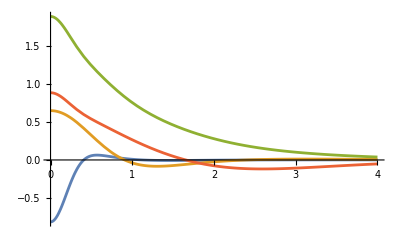

```mathematica
Ψ=#.Array[χ[Subscript[α, #]]&,{4}]&/@ψ;
Plot[Ψ,{r,0,4},PlotRange->All]
```

```mathematica
γ=√(1/π)Exp[-r];(* Ground truth γ for the comparison *)
```

```mathematica
(* Out of all the elements of the list Ψ select the one which has the maximum integral *)
ϕ=Select[Ψ,NIntegrate[Abs[#]^2,{r,0,∞}]==Max[NIntegrate[Abs[#]^2,{r,0,∞}]&/@ Ψ]&]//First;
(* Calculate the normalization for such function *)
η=NIntegrate[4π r^2 Abs[ϕ]^2,{r,0,∞}];
θ=ϕ/(√η)//Simplify
```

0.0961015 ⅇ^(-13.0077 r^2)+0.163017 ⅇ^(-1.96208 r^2)+0.185587 ⅇ^(-0.444529 r^2)+0.0737008 ⅇ^(-0.121949 r^2)

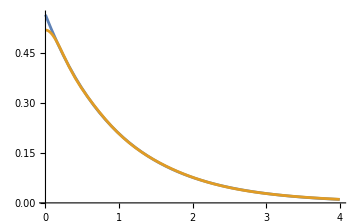
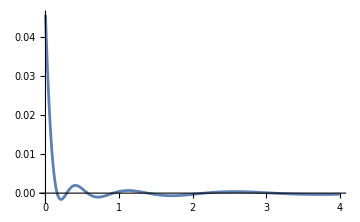

```mathematica
(* Plot of the solution obtained with the BO method compared to the theoretical one, on the side there is the plot of the difference of the functions *)
Plot[#,{r,0,4},PlotRange->Full,ImageSize->Medium]&/@{{γ,θ},γ-θ}
```

```mathematica
γ-θ/.{r->0} (* The maximum difference between the BO approximation with 4 orbitals and the ground truth *)
```

0.0457831